```mathematica
Входные данные;
```

```mathematica
ϵ=0.001;X0={-1,-2};α=100;
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2
antiGradF[{x1_,x2_}]:=-Grad[f[{x,y}],{x,y}]/.{x->x1,y->x2}
NormGradF[{x_,y_}]:=Norm[antiGradF[{x,y}]]
uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
X=X0;
points={X0};
norm={NormGradF[X0]};
κArray={};
γArray={};fValues={f[X0]};
pArray={};
Clear[κ]
```

```mathematica
Метод Флетчера - Ривса;
```

Результат получен за 62 итер.: X = {0.999521, 0.999039}

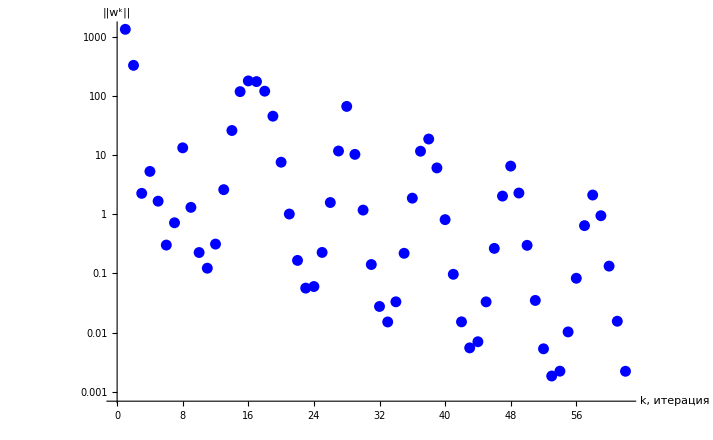

```mathematica
p=antiGradF[X];
κArray=Append[κArray,NArgMin[f[X+κ p],κ]];
X+=κArray[[-1]] p;
points=Append[points,X];
fValues=Append[fValues,f[X]];

While[NormGradF[X]≥ ϵ,
γ = NormGradF[X]^2/NormGradF[points[[-2]]]^2;γArray=Append[γArray,γ];
p = γ p + antiGradF[X];
norm=Append[norm,Norm[p]];
κArray=Append[κArray,NArgMin[f[X+κ p],κ]];
X+=κArray[[-1]] p;
points=Append[points,X];
fValues=Append[fValues,f[X]];


(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

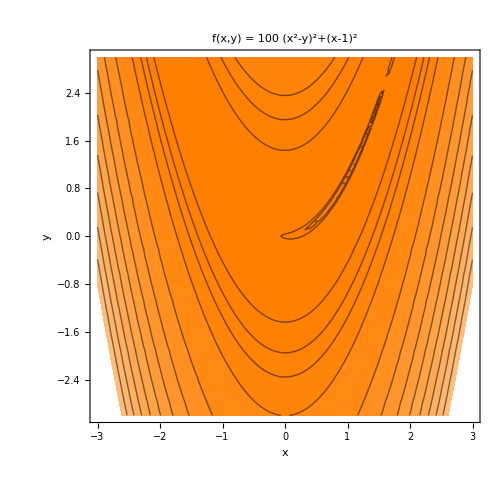

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[20]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500]
```

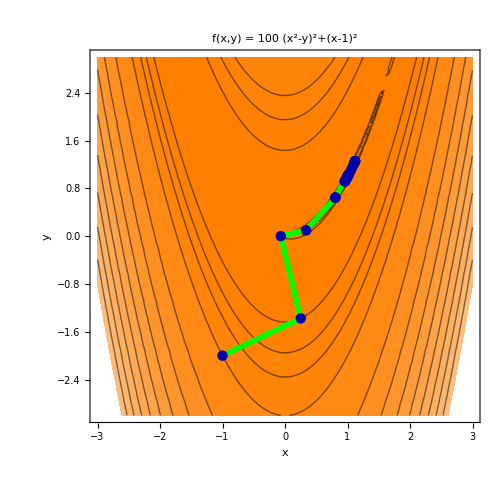

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[8]],fValues[[20]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Green,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
(*gridData[[All,3]]=SetAccuracy[fValues,8];*)
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[κArray,8];
gridData[[All,5]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;10]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 904.0000000 | 0.0010397 | 1345.2197
1 | ( 0.2517682, -1.3761952 ) | 207.7996213 | 0.0042771 | 330.7567499
2 | ( -0.0674279, 0.0019946 ) | 1.1400535 | 0.1842003 | 2.262075
3 | ( 0.3378117, 0.0989424 ) | 0.4615193 | 0.1351326 | 5.3169418
4 | ( 0.8054685, 0.6444038 ) | 0.0397572 | 0.001811 | 1.6680016
5 | ( 0.8047835, 0.6473459 ) | 0.0381204 | 0.0051324 | 0.3019661
6 | ( 0.8061498, 0.6480774 ) | 0.0379019 | 0.9437402 | 0.7194098
7 | ( 1.1169922, 1.2516758 ) | 0.0152906 | 0.0004131 | 13.3141914
8 | ( 1.1201308, 1.2561921 ) | 0.0146562 | 0.0004172 | 1.3111929
... | ... | ... | ... | ...
56 | ( 1.0013140, 1.0025822 ) |       -6
2.0 10 | 0.0024171 | 0.6438857
57 | ( 1.0006369, 1.0011809 ) |       -6
1.3 10 | 0.0008829 | 2.1199547
58 | ( 0.9997887, 0.9995125 ) |      -7
5. 10 | 0.0005031 | 0.9473131
59 | ( 0.9995599, 0.9990944 ) |      -7
3. 10 | 0.0004535 | 0.1329788
60 | ( 0.9995268, 0.9990440 ) |      -7
2. 10 | 0.0004507 | 0.0155543
61 | ( 0.9995217, 0.9990391 ) |      -7
2. 10 | 0.0004757 | 0.0022158

Результат получен за 14 итер.: X = {1., 1.}

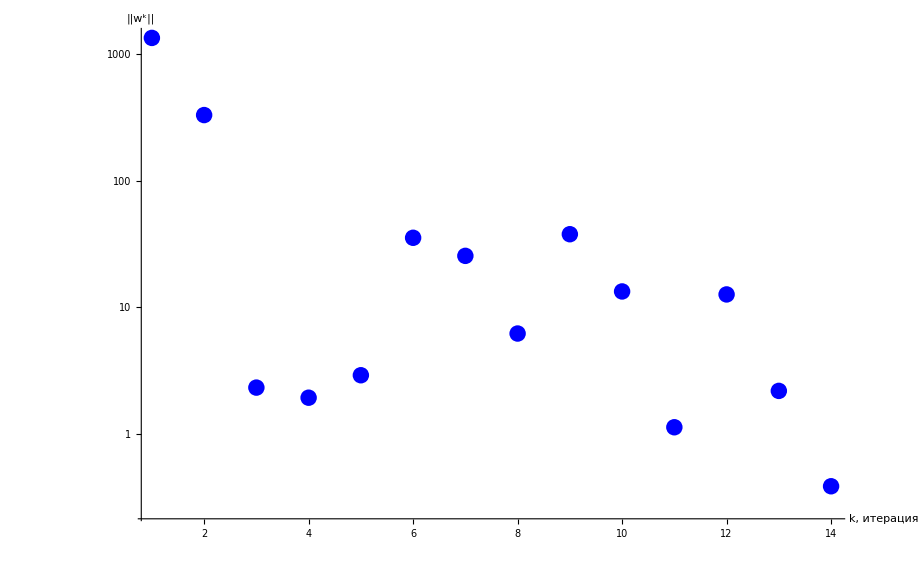

```mathematica
Метод Полака - Рибьера;
X=X0;
points={X0};
norm={NormGradF[X0]};
κArray={};fValues={f[X0]};
p=antiGradF[X];
Clear[κ]
κArray=Append[κArray,NArgMin[f[X+κ p],κ]];
X+=κArray[[-1]] p;
points=Append[points,X];
fValues=Append[fValues,f[X]];

While[NormGradF[X]≥ ϵ,
γ = ((antiGradF[X]-antiGradF[points[[-2]]]).antiGradF[X])/NormGradF[points[[-2]]]^2;γArray=Append[γArray,γ];
p = γ p + antiGradF[X];
norm=Append[norm,Norm[p]];
κArray=Append[κArray,NArgMin[f[X+κ p],κ]];
X+=κArray[[-1]] p;
points=Append[points,X];
fValues=Append[fValues,f[X]];


(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

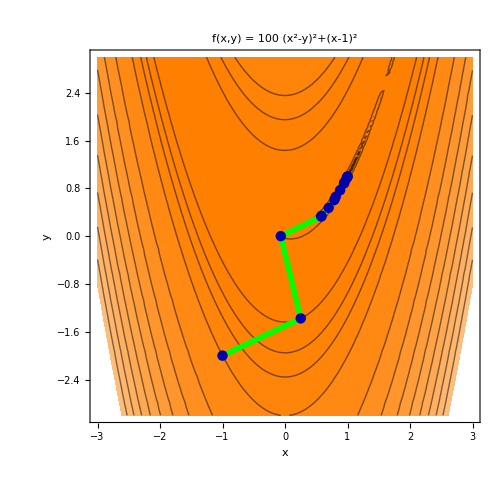

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[4]],fValues[[7]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Green,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[κArray,8];
gridData[[All,5]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;4]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-4;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 904.0000000 | 0.0010397 | 1345.2197
1 | ( 0.2517682, -1.3761952 ) | 207.7996213 | 0.0042771 | 330.7567499
2 | ( -0.0674279, 0.0019946 ) | 1.1400535 | 0.3117119 | 2.3296511
... | ... | ... | ... | ...
8 | ( 0.8818421, 0.7713939 ) | 0.0178695 | 0.0034368 | 37.8977109
9 | ( 0.9447660, 0.8854310 ) | 0.0081657 | 0.0012835 | 13.3843676
10 | ( 0.9495326, 0.9019349 ) | 0.0025574 | 0.0687487 | 1.1326291
11 | ( 0.9860458, 0.9707100 ) | 0.0004432 | 0.0019787 | 12.67697
12 | ( 0.9966168, 0.9934582 ) | 0.0000160 | 0.0030356 | 2.1942753
13 | ( 0.9996994, 0.9993631 ) |      -7
2. 10 | 0.0018266 | 0.3873747

Результат получен за 9 итер.: X = {1., 1.}

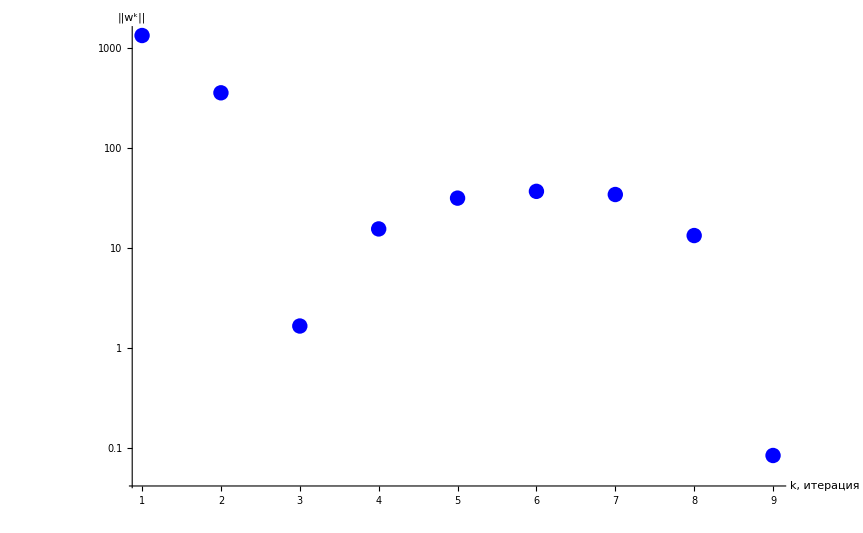

```mathematica
Метод сопряженных градиентов при Q==H(X^k);
X=X0;
points={X0};
norm={NormGradF[X0]};
κArray={};fValues={f[X0]};
p=antiGradF[X];
HesseF[{x1_,y1_}] :=( Grad[Grad[f[{x,y}],{x,y}],{x,y}])/.{x->x1,y->y1};
Clear[κ]
κArray=Append[κArray,NArgMin[f[X+κ p],κ]];
X+=κArray[[-1]] p;
points=Append[points,X];
fValues=Append[fValues,f[X]];

While[NormGradF[X]≥ ϵ,
γ =- ((HesseF[X]. p).antiGradF[X])/((HesseF[X]. p).p);γArray=Append[γArray,γ];
p = γ p + antiGradF[X];
norm=Append[norm,Norm[p]];
κArray=Append[κArray,NArgMin[f[X+κ p],κ]];
X+=κArray[[-1]] p;
points=Append[points,X];
fValues=Append[fValues,f[X]];


(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
];
"Результат получен за "<>ToString[Length[points]-1]<> " итер.: X = "<>ToString[X]
ListLogPlot[norm,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||w^k||"}]
```

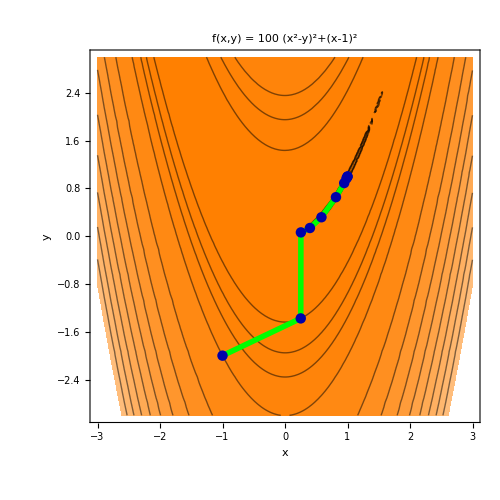

```mathematica
CP0={-3,-3};
ContourPlot[f[{x,y}],{x,CP0[[1]],3},{y,CP0[[2]],3},Contours->uniformMesh[fValues[[1]],0.8(f[CP0]-fValues[[1]]),10]~Join~uniformMesh[fValues[[2]],0.8(fValues[[1]]-fValues[[2]]),2]~Join~fValues[[1;;4]]~Join~{fValues[[3]],fValues[[5]]},ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["f(x,y)",Italic]," = ",f[{x,y}]}],Large],FrameStyle->Thick,ImageSize->500,Epilog->{Green,Thickness[0.008],Line[points],Darker[Blue],PointSize[0.015],Point[points],Black}]
```

```mathematica
len=Length[norm];
gridLabel={"k","X^k","f(X^k)","κ_k","||w^k||"};gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,len}];gridData[[All,1]]=Table[i,{i,0,len-1}];
For[i=1,i≤len,i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],8]]<>", "<>ToString[SetAccuracy[points[[i,2]],8]]<>" )"]
For[i=1,i≤len,i++,gridData[[i,3]]=ToString[SetAccuracy[fValues[[i]],8]]];
gridData[[All,4]]=SetAccuracy[κArray,8];
gridData[[All,5]]=SetAccuracy[norm,8];
gridData={gridLabel}~Join~gridData;
Grid[gridData[[1;;4]]~Join~{Table["...",{i,1,Length[gridLabel]}]}~Join~gridData[[len-3;;len+1]],Dividers->{Table[i->True,{i,1,1+Length[gridLabel]}],True},FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15],Background->{None,{{LightCyan,LightBlue}}}]
```

k | X^k | f(X^k) | κ_k | ||w^k||
0 | ( -1.0000000, -2.0000000 ) | 904.0000000 | 0.0010397 | 1345.2197
1 | ( 0.2517682, -1.3761952 ) | 207.7996213 | 0.0040054 | 359.7409445
2 | ( 0.2543580, 0.0647114 ) | 0.5559820 | 0.0966188 | 1.6762165
... | ... | ... | ... | ...
4 | ( 0.5833482, 0.3184095 ) | 0.2214966 | 0.0128289 | 31.8359683
5 | ( 0.8153147, 0.6545618 ) | 0.0444642 | 0.007282 | 37.220304
6 | ( 0.9470622, 0.8914269 ) | 0.0058273 | 0.0024656 | 34.6029501
7 | ( 0.9835678, 0.9685376 ) | 0.0003982 | 0.0026263 | 13.4547104
8 | ( 0.9999321, 0.9998564 ) |      -7
0. 10 | 0.0018664 | 0.0850725